#### Init Experimental Sim

```mathematica
(* simulating a "standing" condition vs a "supine" condition to see how far a participant will travel *)

(* mostly just a way to show off fitting with uncertainties, and error bands *)
```

```mathematica
nDistances=10;
nSamplesPerDistance=5;
```

```mathematica
distance[i_]:=10*Ceiling[i/nSamplesPerDistance];
spread[i_]:=distance[i]/10;
skew[i_]:=0;
```

0.950986 x+1.55791

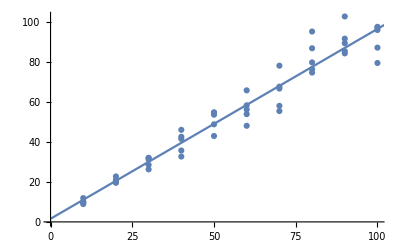

```mathematica
(* true distance travelled is 0.98 metres travelled / target distance *)
dataStanding=Table[{distance[i],   RandomVariate[NormalDistribution[   0.98*distance[i],spread[i]   ]]},{i,1,nDistances*nSamplesPerDistance}];
dataPlotStanding=ListPlot[dataStanding];
fitFnStanding=Fit[dataStanding,{1,x},x]
fitPlotStanding=Plot[fitFnStanding,{x,0,10*(nDistances+1)}];
Show[{dataPlotStanding,fitPlotStanding}]
```

1.0696 x-1.42396

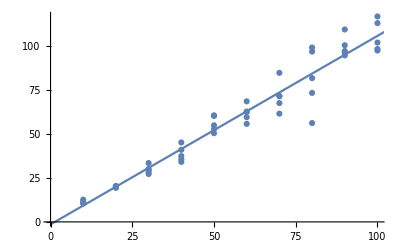

```mathematica
(* true distance travelled is 1.05 metres travelled / target distance *)
dataSupine=Table[{distance[i],   RandomVariate[NormalDistribution[   1.05*distance[i],spread[i]   ]]},{i,1,nDistances*nSamplesPerDistance}];
dataPlotSupine=ListPlot[dataSupine];
fitFnSupine=Fit[dataSupine,{1,x},x]
fitPlotSupine=Plot[fitFnSupine,{x,0,10*(nDistances+1)}];
Show[{dataPlotSupine,fitPlotSupine}]
```

```mathematica
(* very rough understanding of how far people go, on average, in these conditions across all distances*)
Around[dataStanding[[All,2]]//Mean,(dataStanding[[All,2]]//StandardDeviation)/Sqrt[nDistances*nSamplesPerDistance-1]]
Around[dataSupine[[All,2]]//Mean,(dataSupine[[All,2]]//StandardDeviation)/Sqrt[nDistances*nSamplesPerDistance-1]]
```

52.4.

57.4.

#### Standing Means

```mathematica
(* mean distance travelled at each target distance *)
meansStanding=Table[{(i+1)*10,Mean[    Take[dataStanding[[All,2]],{i*nSamplesPerDistance+1,(i+1)*nSamplesPerDistance}]]    },{i,0,nDistances-1}];
(* uncertainty of the mean for each distance travelled *)
uncertaintyStanding=Table[{(i+1)*10,StandardDeviation[    Take[dataStanding[[All,2]],{i*nSamplesPerDistance+1,(i+1)*nSamplesPerDistance}]]/Sqrt[nSamplesPerDistance-1]    },{i,0,nDistances-1}];
dataWithErrorStanding=Table[{        meansStanding[[i,1]],     Around[     meansStanding[[i,2]],uncertaintyStanding[[i,2]]     ]   },{i,1,nDistances}]


fitModelStandingMeans=NonlinearModelFit[meansStanding,m*x+b,{m,b},x,Weights->1/uncertaintyStanding[[All,2]]^2]
fitFnStandingMeans=fitModelStandingMeans["BestFit"]
fitParsStandingMeans=fitModelStandingMeans["ParameterTable"]
```

(10 | 10.10.6
20 | 20.70.6
30 | 30.01.3
40 | 39.82.7
50 | 51.02.6
60 | 56.53.2
70 | 65.4.
80 | 83.4.
90 | 91.4.
100 | 92.4.)

FittedModel[0.970278 x+0.814819]

0.970278 x+0.814819

| Estimate | Standard Error | t-Statistic | P-Value
m | 0.970278 | 0.0215913 | 44.9385 | 6.63883×10^-11
b | 0.814819 | 0.556711 | 1.46363 | 0.181448

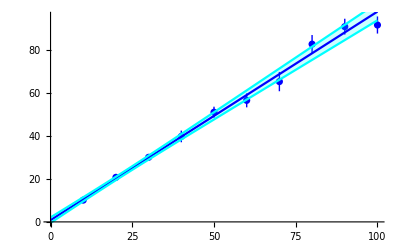

```mathematica
(* plot the means and uncertainties at each distance, fit with weight by uncertainty of the mean, and show error band *)
dataPlotStandingMeans=ListPlot[dataWithErrorStanding,PlotStyle->{Blue}];
bandsPlotStanding=Plot[{fitModelStandingMeans[x],fitModelStandingMeans["MeanPredictionBands",ConfidenceLevel-> 0.95]},{x,0,100},Filling->{2->{1}},PlotStyle->{Blue,Cyan}];
Show[{dataPlotStandingMeans,bandsPlotStanding}]
```

#### Supine Means

```mathematica
meansSupine=Table[{(i+1)*10,Mean[    Take[dataSupine[[All,2]],{i*nSamplesPerDistance+1,(i+1)*nSamplesPerDistance}]]    },{i,0,nDistances-1}];
uncertaintySupine=Table[{(i+1)*10,StandardDeviation[    Take[dataSupine[[All,2]],{i*nSamplesPerDistance+1,(i+1)*nSamplesPerDistance}]]/Sqrt[nSamplesPerDistance-1]    },{i,0,nDistances-1}];
dataWithErrorSupine=Table[{        meansSupine[[i,1]],     Around[     meansSupine[[i,2]],uncertaintySupine[[i,2]]     ]   },{i,1,nDistances}]



fitModelSupineMeans=NonlinearModelFit[meansSupine,m*x+b,{m,b},x,Weights->1/uncertaintySupine[[All,2]]^2]
fitFnSupineMeans=fitModelSupineMeans["BestFit"]
fitParsSupineMeans=fitModelSupineMeans["ParameterTable"]
```

(10 | 11.20.4
20 | 19.970.21
30 | 29.71.2
40 | 38.62.2
50 | 55.72.2
60 | 61.72.3
70 | 71.4.
80 | 81.9.
90 | 99.42.9
100 | 105.4.)

FittedModel[1.03322 x-0.360289]

1.03322 x-0.360289

| Estimate | Standard Error | t-Statistic | P-Value
m | 1.03322 | 0.0354428 | 29.1516 | 2.07618×10^-9
b | -0.360289 | 0.7523 | -0.478916 | 0.644814

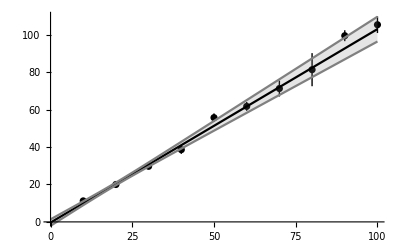

```mathematica
dataPlotSupineMeans=ListPlot[dataWithErrorSupine,PlotStyle->{Black}];
bandsPlotSupine=Plot[{fitModelSupineMeans[x],fitModelSupineMeans["MeanPredictionBands",ConfidenceLevel-> 0.95]},{x,0,100},Filling->{2->{1}},PlotStyle->{Black,Gray}];
Show[{dataPlotSupineMeans,bandsPlotSupine}]
```

#### Ratio of Means

```mathematica
(* trying to show that the "ratio of means" is not a good descriptor of the data *)

(* this is because ratios are not a linear operation, so the ratio of fitted slopes will be different from the average of the ratio of means *)
```

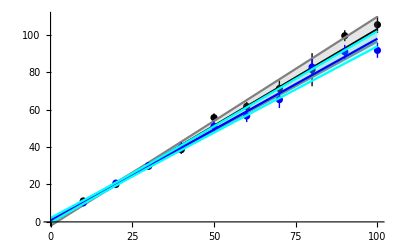

```mathematica
(* show the two fits at once *)
Show[{dataPlotSupineMeans,bandsPlotSupine,dataPlotStandingMeans,bandsPlotStanding}]
```

```mathematica
(* should be equivalent to taking ratios of slopes. Let's see *)
slopeStanding=Around[m/.fitModelStandingMeans["BestFitParameters"],fitModelStandingMeans["ParameterErrors"][[1]] ]
slopeSupine=Around[m/.fitModelSupineMeans["BestFitParameters"],fitModelSupineMeans["ParameterErrors"][[1]] ]

(* ratio of slopes *)
slopeSupine/slopeStanding (* different from 1*)

(* difference of slopes *)
slopeSupine-slopeStanding  (* different from 0 *)
```

0.9700.022

1.0330.035

1.060.04

0.060.04

```mathematica
ratioOfMeans=(dataWithErrorSupine[[All,2]]/dataWithErrorStanding[[All,2]])^1;

meansRatio=Table[{i*10,ratioOfMeans[[i]]["Value"]  },{i,1,nDistances}];
uncertaintyRatio=Table[{i*10,ratioOfMeans[[i]]["Uncertainty"]  },{i,1,nDistances}];
dataWithErrorRatio=Table[{ i*10,     Around[     meansRatio[[i,2]],uncertaintyRatio[[i,2]]     ]   },{i,1,nDistances}]
```

(10 | 1.110.07
20 | 0.9630.031
30 | 0.990.06
40 | 0.970.09
50 | 1.090.07
60 | 1.090.08
70 | 1.090.10
80 | 0.980.12
90 | 1.090.05
100 | 1.150.07)

```mathematica
(* get the average of ratios by fitting *)
fitModelRatioMeans=NonlinearModelFit[meansRatio,b,{b},x,Weights->1/uncertaintyRatio[[All,2]]^2]
fitFnRatioMeans=fitModelRatioMeans["BestFit"]
fitParsRatioMeans=fitModelRatioMeans["ParameterTable"]

averageRatioOfMeans=Around[b/.fitModelRatioMeans["BestFitParameters"],fitModelRatioMeans["ParameterErrors"][[1]] ]
```

FittedModel[1.0288]

1.0288

| Estimate | Standard Error | t-Statistic | P-Value
b | 1.0288 | 0.0229126 | 44.9011 | 6.73979×10^-12

1.0290.023

Notice how the ratio of slopes, 1.060.04 is not the same as the average of ratios, 1.0290.023

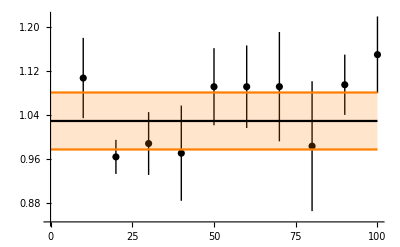

```mathematica
(* show the ratios of means, with uncertainty band *)
dataPlotRatioMeans=ListPlot[dataWithErrorRatio,PlotStyle->{Black}];
fitPlotRatioMeans=Plot[{fitModelRatioMeans[x],fitModelRatioMeans["MeanPredictionBands",ConfidenceLevel-> 0.95]},{x,0,100},Filling->{2->{1}},PlotStyle->{Black,Orange}];
Show[{dataPlotRatioMeans,fitPlotRatioMeans}]
```

```mathematica
Print["Notice how the ratio of slopes, ",slopeSupine/slopeStanding ," is not the same as the average of ratios, ", averageRatioOfMeans]
```

Notice how the ratio of slopes, 1.060.04 is not the same as the average of ratios, 1.0290.023